```mathematica
SetDirectory[NotebookDirectory[]];
data = Import["wolfram_tau_vs_iter.txt","Table"];
```

```mathematica
k = data[[1]][[1]]
```

500

```mathematica
data1 = data[[2;;k+1]];
```

```mathematica
Length@data1
```

500

```mathematica
data2 = data[[k+2;;2*k+1]];
```

```mathematica
Length@data2
```

500

```mathematica
data3 = data[[2*k+2;;3*k+1]];
```

```mathematica
Length@data3
```

500

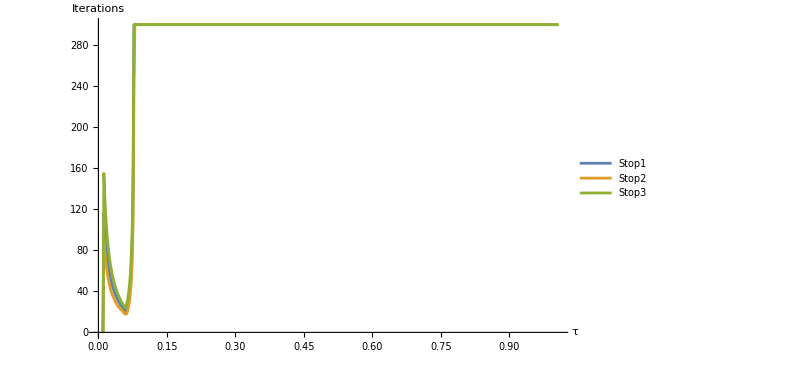

```mathematica
ListLinePlot[{data1,data2,data3},ImageSize->600,PlotLegends->{"Stop1","Stop2","Stop3"},AxesLabel->{"τ","Iterations"}]
```